```mathematica
Clear[number,posfiles,positions,wls,resfiles,wstfiles,fitfiles,resfields,wstfields,fitfields,displacementField,vortexFields]
```

```mathematica
SetDirectory[]
```

/Users/nathaniel

## Find out the max number of files there might be to import

[Header] and [Folder] should end in a ‘/’

```mathematica
Header="Downloads/";
Folder="RunData/";
Pos="Pos/pos";
Res="Resource/rsc";
Wst="Waste/wst";
Fitness="Fitness/fit";
Stat="StatData/";
```

```mathematica
scale=150;
fps=15.;
```

```mathematica
maxRes=4096;
```

```mathematica
write3D=False;
```

```mathematica
animate=True;
```

## Import files

### Create file names

Displacement field animation file names

```mathematica
name=Header<>Folder<>"DisplacementField";
Quiet[dispfieldnum=Length[Import[name]]];
(******)
dispfieldnum=15;
(******)
dispfieldfiles={};
For[i=0,i<dispfieldnum,++i,AppendTo[dispfieldfiles,name<>"/dispField"<>ToString[i]<>".csv"]]
```

Vortex files

```mathematica
name=Header<>Folder<>"Vortex";
Quiet[vortexnum=Length[Import[name]]];
(********)
(*vortexnum=30*)
(********)
vortexfiles={};
For[i=0,i<vortexnum,++i,AppendTo[vortexfiles,name<>"/vortex"<>ToString[i]<>".csv"]]
```

Position file names

```mathematica
Quiet[posnum=Import[Header<>Folder<>"Pos/number.csv"]⟦1⟧⟦1⟧];
If[posnum==$Failed,posnum=0,Null];
If[animate==True,Null,posnum=0]
Print["There are ", posnum, " files to import."]
```

There are 45 files to import.

```mathematica
(********)
(*posnum=30*)
(********)
```

```mathematica
posfiles={};
For[i=0,i<posnum,++i,AppendTo[posfiles,Header<>Folder<>Pos<>ToString[i]<>".csv"]]
```

Column displacement file names

```mathematica
name=Header<>Folder<>"Columns";
Quiet[columnnum=Length[Import[name]]];
columnfiles={};
For[i=0,i<columnnum,++i,AppendTo[columnfiles,name<>"/col"<>ToString[i]<>".csv"]]
```

Resource file names

```mathematica
resfiles={};
For[i=0,i<posnum,++i,AppendTo[resfiles,Header<>Folder<>Res<>ToString[i]<>".csv"]]
```

Waste file names

```mathematica
wstfiles={};
For[i=0,i<posnum,++i,AppendTo[wstfiles,Header<>Folder<>Wst<>ToString[i]<>".csv"]]
```

Fitness file names

```mathematica
fitfiles={};
For[i=0,i<posnum,++i,AppendTo[fitfiles,Header<>Folder<>Fitness<>ToString[i]<>".csv"]]
```

StatData file

```mathematica
statfiles={};
name =Header<>Folder<>Stat<>"statNames.csv";
If[FileExistsQ[name],statfiles=Import[name],Null];
```

StatPlot file

```mathematica
statplotfiles={};
name =Header<>Folder<>"StatPlotData/statNames.csv";If[FileExistsQ[name],statplotfiles=Import[name],Null];
```

Bulk outline files

```mathematica
name=Header<>Folder<>"bulkOutline";
If[FileExistsQ[name],bulknum=Import[name<>"/number.csv"]⟦1⟧⟦1⟧,bulknum=0];
bulkfiles={};
For[i=0,i<bulknum,++i,AppendTo[bulkfiles,Header<>Folder<>"bulkOutline/bulk"<>ToString[i]<>".csv"]]
```

### Import data

Get the positions

```mathematica
positions={};
For[i=1,i≤posnum,++i,If[FileExistsQ[posfiles⟦i⟧],AppendTo[positions,Import[posfiles⟦i⟧]],Null]]
```

Get column displacement

```mathematica
columns={};
For[i=1,i≤columnnum,++i,If[FileExistsQ[columnfiles⟦i⟧],AppendTo[columns,Import[columnfiles⟦i⟧]],Null]]
```

Get bulk field

```mathematica
name=Header<>Folder<>"bulkField.csv";
Quiet[bulkField=Import[name]];
If[bulkField==$Failed,bulkField={},Null];
```

Get bulk outline

```mathematica
outlines={};
For[i=1,i≤bulknum,++i,If[FileExistsQ[bulkfiles⟦i⟧],AppendTo[outlines,Import[bulkfiles⟦i⟧]],Null]]
```

Get displacement field (snapshot)

```mathematica
name=Header<>Folder<>"displacementField.csv";
Quiet[displacementField=Import[name]];
If[displacementField==$Failed,displacementField={},Null];
```

Get displacement field record (animate)

```mathematica
name=Header<>Folder<>"DisplacementField";
dispFields={};
For[i=1,i≤dispfieldnum,++i,If[FileExistsQ[dispfieldfiles⟦i⟧],AppendTo[dispFields,Import[dispfieldfiles⟦i⟧]],Null]]
```

Get vortex field

```mathematica
name=Header<>Folder<>"Vortex";
vortexFields={};
For[i=1,i≤vortexnum,++i,If[FileExistsQ[vortexfiles⟦i⟧],AppendTo[vortexFields,Import[vortexfiles⟦i⟧]],Null]]
```

Get bulk record

```mathematica
Quiet[ bulkVolumes=Import[Header<>Folder<>"bulkVolumes.csv"]];
If[bulkVolumes==$Failed, bulkRecord={},Null];
```

Get pressure field

```mathematica
Quiet[pressField=Import[Header<>Folder<>"pressField.csv"]];
If[pressField==$Failed,pressField={};Null];
```

Get the resource fields

```mathematica
resfields={};
For[i=1,i≤posnum,++i,If[FileExistsQ[resfiles⟦i⟧],AppendTo[resfields,Import[resfiles⟦i⟧]],]]
```

Get the waste fields

```mathematica
wstfields={};
For[i=1,i≤posnum,++i,If[FileExistsQ[wstfiles⟦i⟧],AppendTo[wstfields,Import[wstfiles⟦i⟧]],]]
```

Get the fitness fields

```mathematica
fitfields={};
For[i=1,i≤posnum,++i,If[FileExistsQ[fitfiles⟦i⟧],AppendTo[fitfields,Import[fitfiles⟦i⟧]],]]
```

Get the walls

```mathematica
Quiet[wls=Import[Header<>Folder<>"walls.csv"]];
If[wls==$Failed,wls={},Null];
```

Get the simulation bounds

```mathematica
Quiet[impbnds=Import[Header<>Folder<>"bnds.csv"]];
Quiet[bnds=impbnds⟦1⟧];
If[impbnds==$Failed,bnds={0,4,0,4},bnds=impbnds⟦1⟧];
bounds={{bnds⟦1⟧,bnds⟦2⟧},{bnds⟦3⟧,bnds⟦4⟧}};
If[impbnds==$Failed,bounds={{0,4},{0,4}},bounds={{bnds⟦1⟧,bnds⟦2⟧},{bnds⟦3⟧,bnds⟦4⟧}}];
```

Get stat files

```mathematica
name=Header<>Folder<>Stat;
statdata=Table[If[FileExistsQ[name<>statfiles⟦i⟧⟦1⟧<>".csv"],Import[name<>statfiles⟦i⟧⟦1⟧<>".csv"],Null],{i,1,Length[statfiles]}];
```

Get stat plots

```mathematica
name=Header<>Folder<>"StatPlotData/";
statplot=Table[If[FileExistsQ[name<>statplotfiles⟦i⟧⟦1⟧<>".csv"],Import[name<>statplotfiles⟦i⟧⟦1⟧<>".csv"],Null],{i,1,Length[statplotfiles]}];
```

Get displacement tracking

```mathematica
name=Header<>Folder<>"displacementI.csv";
displacementI=If[FileExistsQ[name],Import[name],{}];
name=Header<>Folder<>"displacementF.csv";
displacementF=If[FileExistsQ[name],Import[name],{}];
```

### Get max values, and the min value of fitness (which can be negative)

```mathematica
max[lst_]:=Max[0,Table[lst⟦i⟧⟦3⟧,{i,1,Length[lst]}]]
min[lst_]:=Min[0,Table[lst⟦i⟧⟦3⟧,{i,1,Length[lst]}]]
mvr=Max[0,Table[max[resfields⟦i⟧],{i,1,Length[resfields]}]];
mvw=Max[0,Table[max[wstfields⟦i⟧],{i,1,Length[wstfields]}]];
mvf=Max[0,Table[max[fitfields⟦i⟧],{i,1,Length[fitfields]}]];
minvf=Min[0,Table[min[fitfields⟦i⟧],{i,1,Length[fitfields]}]];
```

## Create Plots

```mathematica
SaveDirectory=Header<>Folder<>"Output/";
If[posnum>0 || Length[statfiles]>0||Length[statplotfiles]>0||Length[ bulkRecord]>0 || Length[displacement]>0||Length[pressField]>0||Length[displacementField]>0||Length[outlines]>0,Quiet[CreateDirectory[SaveDirectory]],Null];
```

### Export stat data

```mathematica
Min1[lst_]:=Min[Table[lst⟦i⟧⟦1⟧,{i,1,Length[lst]}]];
Max1[lst_]:=Max[Table[lst⟦i⟧⟦1⟧,{i,1,Length[lst]}]];
Min2[lst_]:=Min[Table[lst⟦i⟧⟦2⟧,{i,1,Length[lst]}]];
Max2[lst_]:=Max[Table[lst⟦i⟧⟦2⟧,{i,1,Length[lst]}]];
```

```mathematica
For[i=1,i≤Length[statdata],++i,Export[SaveDirectory<>statfiles⟦i⟧<>".jpg",ListLinePlot[statdata⟦i⟧,ImageSize->{2048,1024},AspectRatio->0.5,PlotRange->If[statfiles⟦i⟧=={"KE"},{0,Max2[statdata⟦i⟧]},All],PlotStyle->{Black},AxesStyle->Directive[Black,24]],"CompressionLevel"->0]];
```

### Export stat plot dat

```mathematica
For[i=1,i≤Length[statplotfiles],++i,Export[SaveDirectory<>statplotfiles⟦i⟧<>".jpg",ListLinePlot[statplot⟦i⟧,ImageSize->{2048,1024},AspectRatio->0.5,PlotRange->{0,Max2[statplot⟦i⟧]},PlotStyle->Black,AxesStyle->Directive[Black,24],PlotRange->All],"CompressionLevel"->0]];
```

### Export bulk data

```mathematica
num=Table[{fps^-1 i,If[ bulkVolumes⟦i⟧=={""},0,Length[ bulkVolumes⟦i⟧]]},{i,1,Length[ bulkVolumes]}];
vol=Table[{fps^-1 i,If[ bulkVolumes⟦i⟧=={""},0,Total[ bulkVolumes⟦i⟧]]},{i,1,Length[ bulkVolumes]}];
```

```mathematica
If[Length[ bulkVolumes]>0,numVoids=ListLinePlot[num,ImageSize->{2048,1024},PlotStyle->Black,AspectRatio->0.5,PlotRange->All,AxesStyle->Directive[Black,24]],Null];
If[Length[ bulkVolumes]>0,volVoids=ListLinePlot[vol,ImageSize->{2048,1024},PlotStyle->Black,AspectRatio->0.5,PlotRange->All,AxesStyle->Directive[Black,24]],Null];
```

```mathematica
If[Length[ bulkVolumes]>0,Export[SaveDirectory<>"NumVoid.jpg",numVoids,"CompressionLevel"->0],Null];
If[Length[ bulkVolumes]>0,Export[SaveDirectory<>"VolVoid.jpg",volVoids,"CompressionLevel"->0],Null];
```

### Export bulk outlines

Process data

```mathematica
lines=Table[Table[
Line[{{outlines⟦i⟧⟦j⟧⟦1⟧,outlines⟦i⟧⟦j⟧⟦2⟧},{outlines⟦i⟧⟦j⟧⟦3⟧,outlines⟦i⟧⟦j⟧⟦4⟧}}],
{j,1,Length[outlines⟦i⟧]}],
{i,1,Length[outlines]}];
```

```mathematica
lineframes=Table[Graphics[lines⟦i⟧],{i,1,Length[lines]}];
```

```mathematica
If[Length[lines]>0,Export[SaveDirectory<>"bulkOutline.avi",lineframes,"CompressionLevel"->0],Null]
```

### Export bulk field

```mathematica
minX=Min1[bulkField];
maxX=Max1[bulkField];
minY=Min2[bulkField];
maxY=Max2[bulkField];
width=maxX-minX;
height=maxY-minY;
Quiet[If[width>height,wX=maxRes;wY=maxRes*height/width,wX=maxRes*width/height;wY=maxRes]];
```

```mathematica
bulkLst=Table[bulkField⟦i⟧⟦3⟧,{i,1,Length[bulkField]}];
minZ=Min[bulkLst];
maxZ=Max[bulkLst];
```

```mathematica
(*CF[z_]:=RGBColor[Mod[5z,256],Mod[17z,256],Mod[15z,256]]*)
```

```mathematica
CF[z_]:=RGBColor[z,1-Sin[π z],Cos[π/2 z]]
```

```mathematica
Plot[{z,Sin[π z],Cos[π/2 z]},{z,0,1},PlotStyle->{Red,Green,Blue}];
```

```mathematica
Table[CF[x],{x,0,1,0.01}];
```

```mathematica
blkFld=If[Length[ bulkField]>0,Show[ListDensityPlot[bulkField,ColorFunction->"SouthwestColors",PlotLegends->Automatic,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All],ImageSize->{wX,wY}],{}];
```

```mathematica
If[Length[ bulkField]>0,Export[SaveDirectory<>"bulkField.jpg",blkFld,"CompressionLevel"->0],Null];
```

### Export pressure field

```mathematica
minX=Min1[pressField];
maxX=Max1[pressField];
minY=Min2[pressField];
maxY=Max2[pressField];
width=maxX-minX;
height=maxY-minY;
Quiet[If[width>height,wX=maxRes;wY=maxRes*height/width,wX=maxRes*width/height;wY=maxRes]];
```

```mathematica
(*,ColorFunction->"SouthwestColors"*)
```

```mathematica
prsField=If[Length[pressField]>0,Show[ListDensityPlot[pressField,PlotLegends->Automatic,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All],ImageSize->{wX,wY}],{}];
```

```mathematica
If[Length[pressField]>0,Export[SaveDirectory<>"pressureField.jpg",prsField,"CompressionLevel"->0],Null];
```

### Export displacement field (snapshot)

```mathematica
maxResD=4096;
```

```mathematica
func[x_]=Log[1+x];
```

```mathematica
minX=Min1[displacementField];
maxX=Max1[displacementField];
minY=Min2[displacementField];
maxY=Max2[displacementField];
width=maxX-minX;
height=maxY-minY;
Quiet[If[width>height,wX=maxRes;wY=maxResD*height/width,wX=maxResD*width/height;wY=maxResD]];
```

```mathematica
dispFieldLog=Table[{displacementField⟦i⟧⟦1⟧,displacementField⟦i⟧⟦2⟧,func[displacementField⟦i⟧⟦3⟧]},{i,1,Length[displacementField]}];
```

```mathematica
dspField=If[Length[displacementField]>0,Show[ListDensityPlot[displacementField,ColorFunction->"SouthwestColors",PlotLegends->Automatic,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All],ImageSize->{wX,wY}],{}];
```

```mathematica
(*dspField=If[Length[displacementField]>0,ListDensityPlot[displacementField,ColorFunction->"SouthwestColors",PlotLegends->Automatic,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All,ImageSize->{wX,wY}],{}];*)
```

```mathematica
dspFieldLog=If[Length[dispFieldLog]>0,Show[ListDensityPlot[dispFieldLog,ColorFunction->"SouthwestColors",PlotLegends->Automatic,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All],ImageSize->{wX,wY}],{}];
```

```mathematica
If[Length[displacementField]>0,Export[SaveDirectory<>"displacementField.jpg",dspField,"CompressionLevel"->0],Null];
```

```mathematica
If[Length[displacementField]>0,Export[SaveDirectory<>"displacementFieldLog.jpg",dspFieldLog,"CompressionLevel"->0],Null];
```

### Export displacement

```mathematica
colf[x_]=Log[x+1];
```

```mathematica
maxResD=4096;
```

```mathematica
minX=bnds⟦1⟧;
maxX=bnds⟦2⟧;
minY=bnds⟦3⟧;
maxY=bnds⟦4⟧;
width=maxX-minX;
height=maxY-minY;
If[width>height,wX=maxResD;wY=maxResD*height/width,wX=maxResD*width/height;wY=maxResD];
```

```mathematica
maxc[lst_]:=Max[Table[colf[lst⟦i⟧⟦6⟧],{i,1,Length[lst]}]]
minc[lst_]:=Min[Table[colf[lst⟦i⟧⟦6⟧],{i,1,Length[lst]}]]
maxC=maxc[displacementI];
minC=minc[displacementI];
diffC =maxC-minC;
```

```mathematica
color[x_]:=RGBColor[(colf[x]-minC)/diffC,0,0]
col[f_]:=If[maxC==0,Black,color[f]];
```

```mathematica
dsk[tr_]:={col[tr⟦6⟧],Disk[{tr⟦1⟧,tr⟦2⟧},tr⟦3⟧]};
```

```mathematica
walls=Graphics[Table[{Blue,Thick,Line[{{wls⟦i⟧⟦1⟧,wls⟦i⟧⟦2⟧},{wls⟦i⟧⟦3⟧,wls
⟦i⟧⟦4⟧}}]},{i,1,Length[wls]}],PlotRange->bounds,ImageSize->{wX,wY}];
```

```mathematica
disksI=Graphics[Table[dsk[displacementI⟦i⟧],{i,1,Length[displacementI]}]];
disksF=Graphics[Table[dsk[displacementF⟦i⟧],{i,1,Length[displacementF]}]];
```

```mathematica
displacementframesI=Show[disksI,walls,PlotRange->bounds,ImageSize->{wX,wY}];
displacementframesF=Show[disksF,walls,PlotRange->bounds,ImageSize->{wX,wY}];
```

```mathematica
If[Length[displacementI]>0,Export[SaveDirectory<>"displacementI.jpg",displacementframesI,"CompressionLevel"->0],Null];
If[Length[displacementF]>0,Export[SaveDirectory<>"displacementF.jpg",displacementframesF,"CompressionLevel"->0],Null];
```

Just something to look at.

```mathematica
dispData=Table[displacement⟦i⟧⟦6⟧,{i,1,Length[displacement]-1}];
Histogram[dispData,200,ImageSize->Large,ScalingFunctions->"Log"];
```

### Export positions

Position data: { x, y, sigma, theta, interaction, ‘color’ }

Color scaling function

```mathematica
colf[x_]=x;
```

Colors

```mathematica
maxc[lst_]:=Max[Table[colf[lst⟦i⟧⟦j⟧⟦6⟧],{i,1,Length[lst]},{j,1,Length[lst⟦i⟧]}]]
minc[lst_]:=Min[Table[colf[lst⟦i⟧⟦j⟧⟦6⟧],{i,1,Length[lst]},{j,1,Length[lst⟦i⟧]}]]
maxC=maxc[positions];
minC=minc[positions];
diffC =maxC-minC;
col[f_]:=If[maxC==0,Black,RGBColor[(colf[f]-minC)/diffC,0,0]];
```

Image size

```mathematica
maxRes=2048;
```

```mathematica
minX=bnds⟦1⟧;
maxX=bnds⟦2⟧;
minY=bnds⟦3⟧;
maxY=bnds⟦4⟧;
width=maxX-minX;
height=maxY-minY;
If[width>height,wX=maxRes;wY=maxRes*height/width,wX=maxRes*width/height;wY=maxRes];
```

Shape definitions

```mathematica
dsk[tr_]:={col[tr⟦6⟧],Disk[{tr⟦1⟧,tr⟦2⟧},tr⟦3⟧]};
odsk[tr_]:={{col[tr⟦5⟧],{Disk[tr⟦1⟧,tr⟦2⟧]}},{Blue,Line[{tr[[1]],tr[[1]]+tr⟦2⟧,{Cos[tr[[3]]],Sin[tr[[3]]]}}]}};
```

```mathematica
walls=Table[{Blue,Thickness[0.01],Line[{{wls⟦i⟧⟦1⟧,wls⟦i⟧⟦2⟧},{wls⟦i⟧⟦3⟧,wls
⟦i⟧⟦4⟧}}]},{i,1,Length[wls]}];
```

```mathematica
disks=Table[Graphics[Join[Table[dsk[positions⟦i⟧⟦j⟧],{j,1,Length[positions⟦i⟧]}],walls],PlotRange->bounds,ImageSize->{wX,wY}],{i,1,Length[positions]}];
```

```mathematica
(*posframes=Table[Show[disks⟦i⟧,walls],{i,1,Length[disks]}];*)
```

```mathematica
(*If[0<Length[posframes],Export[SaveDirectory<>"positions.avi",posframes,"CompressionLevel"->0]];*)
```

```mathematica
If[0<Length[disks],If[Length[disks]==1,Export[SaveDirectory<>"positions.jpg",disks⟦1⟧,"CompressionLevel"->0],Export[SaveDirectory<>"positions.avi",disks,"CompressionLevel"->0]]];
```

### Export resource fields

```mathematica
If[write3D,resframes=Table[ListPlot3D[resfields⟦i⟧,PlotRange->{0,mvr},ImageSize->Large],{i,1,Length[resfields]}],Null];
```

```mathematica
If[write3D,If[0<Length[resframes],Export[SaveDirectory<>"resource.avi",resframes,"CompressionLevel"->0],Null],Null];
```

```mathematica
resdframes=Table[ListDensityPlot[resfields⟦i⟧,PlotRange->{0,mvr},ImageSize->Large,InterpolationOrder->0],{i,1,Length[resfields]}];
```

```mathematica
If[0<Length[resdframes],Export[SaveDirectory<>"resDensity.avi",resdframes,"CompressionLevel"->0]];
```

### Export waste fields

```mathematica
If[write3D,wstframes=Table[ListPlot3D[wstfields⟦i⟧,PlotRange->{0,mvw},ImageSize->Large],{i,1,Length[wstfields]}],Null];
```

```mathematica
If[write3D,If[0<Length[wstframes],Export[SaveDirectory<>"waste.avi",wstframes,"CompressionLevel"->0]],Null];
```

```mathematica
wstdframes=Table[ListDensityPlot[wstfields⟦i⟧,PlotRange->{0,mvw},ImageSize->Large,InterpolationOrder->0],{i,1,Length[wstfields]}];
```

```mathematica
If[0<Length[wstdframes],Export[SaveDirectory<>"wstDensity.avi",wstdframes,"CompressionLevel"->0]];
```

### Export fitness fields

```mathematica
If[write3D,fitframes=Table[ListPlot3D[fitfields⟦i⟧,PlotRange->{0,mvf},ImageSize->Large],{i,1,Length[fitfields]}],Null];
```

```mathematica
If[write3D,If[0<Length[fitframes],Export[SaveDirectory<>"fitness.avi",fitframes,"CompressionLevel"->0],Null],Null];
```

```mathematica
fitdframes=Table[ListDensityPlot[fitfields⟦i⟧,PlotRange->{minvf,mvf},ImageSize->Large,InterpolationOrder->0],{i,1,Length[fitfields]}];
```

```mathematica
If[0<Length[fitdframes],Export[SaveDirectory<>"fitDensity.avi",fitdframes,"CompressionLevel"->0],Null];
```

### Export displacement field animation

Don’t do this

```mathematica
maxResD=4096;
```

```mathematica
func[x_]=Log[1+x];
```

```mathematica
Quiet[minX=Min1[dispFields⟦1⟧]];
Quiet[maxX=Max1[dispFields⟦1⟧]];
Quiet[minY=Min2[dispFields⟦1⟧]];
Quiet[maxY=Max2[dispFields⟦1⟧]];
width=maxX-minX;
height=maxY-minY;
Quiet[If[width>height,wX=maxRes;wY=maxResD*height/width,wX=maxResD*width/height;wY=maxResD]];
```

```mathematica
fdispField={};
If[Length[displacementField]>0,For[i=1,i<dispfieldnum,++i,AppendTo[fdispField,Table[{displacementField⟦i⟧⟦1⟧,displacementField⟦i⟧⟦2⟧,func[displacementField⟦i⟧⟦3⟧]},{i,1,Length[displacementField]}]]],Null];
```

```mathematica
dspFieldAnimation=Table[ListDensityPlot[fdispField⟦i⟧,AspectRatio->Automatic,ColorFunction->"SouthwestColors"],{i,1,Length[fdispField]}];
```

```mathematica
If[Length[dspFieldAnimation]>0,Export[SaveDirectory<>"dispFieldEvolution.avi",dspFieldAnimation,"CompressionLevel"->0],Null];
```

### Export vortex fields

```mathematica
maxResD=4096;
```

```mathematica
func[x_]=Log[1+x];
```

```mathematica
Quiet[minX=Min1[vortexFields⟦1⟧]];
Quiet[maxX=Max1[vortexFields⟦1⟧]];
Quiet[minY=Min2[vortexFields⟦1⟧]];
Quiet[maxY=Max2[vortexFields⟦1⟧]];
width=maxX-minX;
height=maxY-minY;
Quiet[If[width>height,wX=maxRes;wY=maxResD*height/width,wX=maxResD*width/height;wY=maxResD]];
```

```mathematica
vortexFrames={};
For[i=1,i≤Length[vortexFields],++i,AppendTo[vortexFrames,ListDensityPlot[vortexFields⟦i⟧,AspectRatio->Automatic,InterpolationOrder->0,PlotRange->All,ImageSize->Large]]]
```

```mathematica
If[Length[vortexFrames]>0,Export[SaveDirectory<>"vortexFields.avi",vortexFrames,"CompressionLevel"->0],Null];
```

### Export column data

```mathematica
dirname=SaveDirectory<>"Columns/";
Quiet[CreateDirectory[dirname]]
```

/Users/nathaniel/Downloads/RunData/Output/Columns/

```mathematica
columnplots={};
For[i=1,i≤Length[columns],++i,AppendTo[columnplots,Show[Plot[x,{x,0,Max[columns⟦1⟧]},PlotStyle->Red],ListPlot[columns⟦i⟧,AspectRatio->1,ImageSize->{1024,1024},PlotStyle->Black]]]]
```

```mathematica
For[i=1,i≤Length[columns],++i,Export[dirname<>"col"<>ToString[i]<>".jpg",columnplots⟦i⟧,"CompressionLevel"->0]]
```

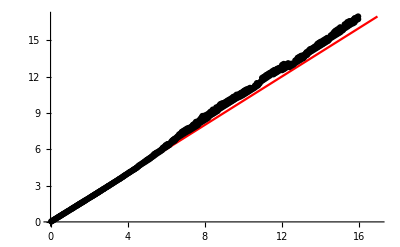

```mathematica
columnplots⟦1⟧
```